```mathematica
Integrate[-8 Cos[ϕ]^2 Sin[ϕ]+8 Sin[ϕ]^2 Cos[ϕ],{ϕ,0,Pi/2}]+
Integrate[24 t^2+t^2,{t,0,1}]
Integrate[-4t Sin[t]Cos[t] √(4 Cos[t]^2+1+4 Sin[t]^2),{t,0,Pi}]
```

25/3

√5 π

```mathematica
Integrate[√((1-Cos[t])^2(1+Sin[t])^2),{t,0,2Pi}]
```

2 π

```mathematica
(* The substance may leave Ω only from the boundry ∂Ω *) 
(* If j is the flow then j.n is the amount leaving at some point of ∂Ω *) 
r[t_]:={Cos[t],Sin[t]};
n[t_]:=Normalize[r[t]]
j[t_]:={2 Cos[t]+Sin[t],Cos[t]};
Integrate[j[t].n[t],{t,0,2Pi}]
```

2 π

True

16

16

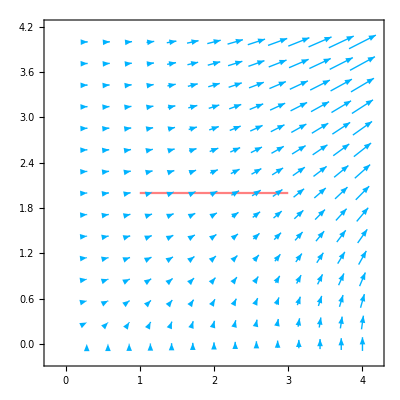

```mathematica
Field[x_,y_]:={2x y,x^2}
PotentialF[x_,y_]:=x^2 y
(*The field is conservative*)
∇_{x,y} PotentialF[x,y] == Field[x,y]
(*Since the path does not matter we can compute the integral on a straight line*)
Integrate[4(1+t),{t,0,2}]
(*Which is the same as applying Newton-Leibniz*)
PotentialF[3,2]-PotentialF[1,2]

Show[{
VectorPlot[Field[x,y],{x,0,4},{y,0,4},VectorStyle->Blend[{Blue,Cyan},0.7]],
Plot[2,{x,1,3},PlotStyle->Pink]
}]
```